## Import Solar Data and constants

```mathematica
SetDirectory[NotebookDirectory[]];

input=Import["anninput"];
If[FileExistsQ["ann"],DeleteFile["ann"]]
build = input[[1,2]];
inmχ=input[[2,2]];
inmA=input[[3,2]];
inep=input[[5,2]];
inαχ=If[StringMatchQ[ToString[input[[4,2]]],"thermal"],0.022 inmχ/1000,input[[4,2]]];


k=2.5; (*See 1602.01465 Eq. 15/16 for what these constants are*)
u0 = 245 10^3; 
uS=233 10^3;
vgal = 550 10^3;(*Galactic escape velocity*)
SR=6.957 10^8;(*Solar radius*)
ρχ=0.3 10^6(*Local dark matter density; PDG says 0.3 GeV/c^2 per cm^-3 = 10^6*0.3 GeV/c^2 per m^-3 *);
Gconst=6.67408 10^-11;
SSM=Import["data/SSM.dat"];
(*The lighter elements seem to have density as a function of radius, so I pulled these functions from *)
(*NB These appear to be mass fractions, not fraction by number. If the second entry is divided by the mass number then it will be fraction by number.*)
Hab=Table[{SSM[[i,2]]*SR,SSM[[i,7]]},{i,2,Length[SSM]}];
He4ab=Table[{SSM[[i,2]]*SR,SSM[[i,8]](*/4*)},{i,2,Length[SSM]}];
He3ab=Table[{SSM[[i,2]]*SR,SSM[[i,9]](*/3*)},{i,2,Length[SSM]}];
C12ab=Table[{SSM[[i,2]]*SR,SSM[[i,10]](*/12*)},{i,2,Length[SSM]}];
N14ab=Table[{SSM[[i,2]]*SR,SSM[[i,11]](*/14*)},{i,2,Length[SSM]}];
O16ab=Table[{SSM[[i,2]]*SR,SSM[[i,12]](*/16*)},{i,2,Length[SSM]}];
Habf=Interpolation[Hab];
He4abf=Interpolation[He4ab];
He3abf=Interpolation[He3ab];
C12abf=Interpolation[C12ab];
N14abf=Interpolation[N14ab];
O16abf=Interpolation[O16ab];

(*Solar mass density importing data*)
SMD=Import["data/SolarMassDensity.csv"](*//ToExpression*)(*r/R_⊙, kg/m^3*);
SMDtab=Table[{SMD[[i,1]]*SR,SMD[[i,2]]},{i,1,Length[SMD]}];
SMDi=Interpolation[SMDtab,InterpolationOrder->1];
SM=NIntegrate[SMDi[x]4π x^2,{x,0,SR}];
(*Htnf is the total fraction by number of hydrogen in the sun*)
Htnf=0.912;
(*Htmf is the total fraction by mass of hydrogen in the sun*)
Htmf=0.710;
(*Total number of atoms in the sun*)
tn=(Htmf*SM)/(1.007825 au Htnf)/.{au->1.660539 10^-27(*kg*)};

(*The function ndtf takes the astrophysical parameter logϵX for a particular element in the sun and outputs the total number density fraction of the sun (e.g. what fraction of the sun is that element by number). The values are taken from 1405.0279 and 1405.0287*)
tnf[logϵX_]:=10^logϵX/10^12 Htnd;
logϵ={(*Mg*) 7.59, (*Si*) 7.51, (*P*) 5.41, (*S*) 7.12, (*K*) 5.04, (*Ca*) 6.32, (*Sc*) 3.16, (*Ti*) 4.93, (*V*) 3.89, (*Cr*) 5.62, (*Mn*) 5.42, (*Fe*) 7.47, (*Co*) 4.93, (*Ni*) 6.20};
(*Table of constant number densities for heavier atoms, number/m^3*)
ndtab=Table[tnf[logϵ⟦i⟧],{i,1,Length[logϵ]}]*tn/(4/3 π SR^3);

(*These are number densities of atoms, number/m^3, radius dependent*)
Hnd[x_]:=SMDi[x]Habf[x]/Hmass/.{Hmass-> 1.007825 au}/.{au->1.660539 10^-27(*kg*)}
He4nd[x_]:=SMDi[x]He4abf[x]/Hmass/.{Hmass-> 4.002602 au}/.{au->1.660539 10^-27(*kg*)}
He3nd[x_]:=SMDi[x]He3abf[x]/Hmass/.{Hmass-> 3.0160293 au}/.{au->1.660539 10^-27(*kg*)}
C12nd[x_]:=SMDi[x]C12abf[x]/Hmass/.{Hmass-> 12 au}/.{au->1.660539 10^-27(*kg*)}
N14nd[x_]:=SMDi[x]N14abf[x]/Hmass/.{Hmass-> 14.003074 au}/.{au->1.660539 10^-27(*kg*)}
O16nd[x_]:=SMDi[x]O16abf[x]/Hmass/.{Hmass-> 15.994915 au}/.{au->1.660539 10^-27(*kg*)}
nd[y_,i_]:=Join[{Hold[Hnd[x]],Hold[He4nd[x]],Hold[He3nd[x]],Hold[C12nd[x]],Hold[N14nd[x]],Hold[O16nd[x]]},ndtab]⟦i⟧/.{x-> y}//ReleaseHold;
(*These lists are for:
{1 H1, 2 He4, 3 He3, 4 C12, 5 N14, 6 O16, 7 Mg, 8 Si, 9 P, 10 S, 11 K, 12 Ca, 13 Sc, 14 Ti, 15 V, 16 Cr, 17 Mn, 18 Fe, 19 Co, 20 Ni}*)
ZN:={1,2,2,6,7,8,12,14,15,16,19,20,21,22,23,24,25,26,27,28};
mN:={1.007825 ,4.002602,3.0160293,12,14.003074,15.994915,24.305, 28.085,30.974,32.06,39.098,40.078,44.956,47.867,50.942,51.996,54.938,55.845,58.933,58.693}au/.{au-> 0.9314941 (*GeV*)};
AN:={1,4,3,12,14,16,24,28,31,32,39,40,45,48,51,52,55,56,59,59};
(*LogLogPlot[{Hnd[r],He4nd[r],He3nd[r],C12nd[r],N14nd[r],O16nd[r],Mgnd[r],Sind[r]},{r,0,SR}]*)
```

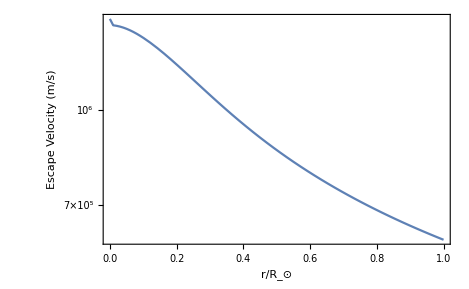

```mathematica
LogPlot[vei[x SR],{x,0,1},Frame-> True,FrameStyle-> Black,LabelStyle-> 10,FrameLabel-> {"r/R_⊙","Escape Velocity (m/s)"},PlotRange-> {{0,1},All}]
```

## Generating Functions

### Generate Escape Velocity

```mathematica
If[build==1,
Mtab=Table[{r,NIntegrate[SMDi[rp]4π rp^2,{rp,0,r}]},{r,0,SR,SR/100.}];
Mi=Interpolation[Mtab,InterpolationOrder->1];
Export["data/Mass.csv",Mtab,"CSV"];
vetab= Table[{r,√(-2(NIntegrate[(Gconst Mi[rp])/rp^2,{rp,SR,r}]-(Gconst Mi[SR])/SR))},{r,SR/100,SR,SR/100}];
vetab=Prepend[vetab,{0.0001,√(-2(NIntegrate[(Gconst Mi[rp])/rp^2,{rp,SR,0.001}]-(Gconst Mi[SR])/SR))}];
Export["data/Escape.csv",vetab,"CSV"];]
```

### Generate fS

```mathematica
If[build==1,
fnonorm[u_]:=(*norm*) (Exp[(vgal^2-u^2)/(k u0^2)]-1)^k HeavisideTheta[vgal-u];
(*normconstant=1/NIntegrate[fnonorm[√(x^2+y^2+z^2)],{x,0,vgal},{y,0,vgal},{z,0,vgal}]*)
normconstant=1/NIntegrate[4π u^2 fnonorm[u],{u,0,vgal}];

f[u_]:=normconstant(Exp[(vgal^2-u^2)/(k u0^2)]-1)^k HeavisideTheta[vgal-u];
usolve=Solve[u^2+uS^2+2u uS c==vgal^2,u][[2]];
upint=u/.usolve/.{c->-1};
Export["data/upint.csv",upint,"CSV"];
fS[u_] := 1/2 NIntegrate[f[√(u^2+uS^2+2u uS c)],{c,-1,1}];
ftab=Table[{u,f[u]},{u,0.,upint,upint/1000}];
Export["data/f.csv",ftab,"CSV"];
fStab=Table[{u,fS[u]},{u,0.,upint,upint/1000}];
Export["data/fS.csv",fStab,"CSV"];]
```

### Generate Integrals

```mathematica
If[build==1,
fStab=Import["data/fS.csv"]//ToExpression;
fSi=Interpolation[fStab];
vetab=Import["data/Escape.csv"]//ToExpression;
vei=Interpolation[vetab,InterpolationOrder->1];
nint1=NIntegrate[4π u(u^2)fSi[u],{u,0,upint}];
Export["data/nint1.csv",nint1,"CSV"];
nint2=NIntegrate[4π u fSi[u],{u,0,upint}];
Export["data/nint2.csv",nint2,"CSV"];
wint[r_]:=nint1+vei[r]^2 nint2;
wrint=NIntegrate[4 π r^2 O16nd[r]wint[r],{r,0,SR}];
Export["data/wrint.csv",wrint,"CSV"];]
```

### Generate Ei

```mathematica
If[build==1,
Ea[z_]:=-NIntegrate[Exp[-t]/t,{t,-z,∞}];
Etab=Table[{-Exp[lnz],Ea[-Exp[lnz]]},{lnz,-10,10,0.1}];
Export["data/Ei.csv",Etab,"CSV"];]
```

## Actual Program

```mathematica
vetab=Import["data/Escape.csv"]//ToExpression;
vei=Interpolation[vetab,InterpolationOrder->1];
fStab=Import["data/fS.csv"]//ToExpression;
fSi=Interpolation[fStab];
ftab=Import["data/f.csv"]//ToExpression;
fi=Interpolation[ftab];
nint1=Import["data/nint1.csv"][[1,1]]//ToExpression;
nint2=Import["data/nint2.csv"][[1,1]]//ToExpression;
wrint=Import["data/wrint.csv"][[1,1]]//ToExpression;
upint=Import["data/upint.csv"][[1,1]]//ToExpression;
Etab=Import["data/Ei.csv"]//ToExpression;
Ei=Interpolation[Etab];
Mtab=Import["data/Mass.csv"]//ToExpression;
Mi=Interpolation[Mtab];
Emax[r_,u_,mχ_,mn_]:=(*1./GeV*)(*Desired units of GeV*)(2 μN^2(*GeV^2/c^4*)( u^2+vei[r]^2)(*m^2/s^2*))/(mn (*GeV/c^2*))1/c^2/.{μN-> (mχ mn)/(mχ+mn),c->3 10^8};
(*AbsoluteTiming[Emax[tr,tu,tmχ,tmN]]*)
Emin[r_,u_,mχ_,mn_]:=(*1./GeV*)(*Desired units of GeV*)1/2 mχ (1(*GeV*))/c^2 u^2  (*m^2/s^2*)/.{c-> 3 10^8(*m/s*)};
(*AbsoluteTiming[Emin[tr,tu,tmχ,tmN]]*)

(*This finds an upper limit on u based on the heaviside theta*)
(*Solve[Emax[SR,u,mχ,Nt]-Emin[SR,u,mχ,Nt]==0,u]*)
(*/.{mχ-> inmχ,Nt-> mNt}*)
upintHS[mχ_,mNu_]:=((0.+8.439776214093713*^6 ) √mχ √mNu)/((mχ+mNu) √(9.-(36. mχ mNu)/(mχ+mNu)^2));

EN[An_]:=(*1/GeV*)(*Desired units of GeV*)0.114/An^(5/3) (*GeV*);
tσSI = 7.542 10^-5 pb /.{pb-> 10^-36 cm^2};
tσSD = 0;
Γcap=1/s 5.9 10^22 ((100 GeV)/(tmχ GeV))^2((270 km/s)/(u0 m/s))^3(tσSI 1200)/(10^-40 cm^2)/.{km->1000m};
(*tu=1/2. vgal;
tmχ=1000.;
tmN=1;
tAN=1;
tmA=0.5;
tr=1 10^6;
tϵ=10^-8;
tαχ=0.035 tmχ/1000;*)
integrandr[r_,i_]:=4π r^2 nd[r,i];
integrandu[r_,u_]:=4π u(u^2+vei[r]^2)fSi[u];
dσdE[r_,u_,mχ_,mA_,ϵ_,αχ_,ER_,mn_,Zn_,En_]:= 8 π ϵ^2 αχ α Zn^2 mn/((u^2+vei[r]^2)(2mn ER +mA^2)^2)Exp[-ER/En] ℏ^2 c^4/.{α-> 1/137.}/.{ℏ-> 6.582119 10^-22 0.001 }/.{c-> 3 10^8};
(*dσdE[tmχ,tmN,tAN,tmA,tϵ,tαχ,tr,tu,Emax[tu,tmχ,tmN,tr]] 10^-4 10^5*)

CNcap[mχ_,mA_,ϵ_,αχ_,i_]:=nχ Block[ {mNt,ZNt,ANt,ENt},
mNt=mN[[i]];
ZNt=ZN[[i]];
ANt=AN[[i]];
ENt=EN[ANt];
NIntegrate[
integrandr[r,i]integrandu[r,u]dσdE[r,u,mχ,mA,ϵ,αχ,ER,mNt,ZNt,ENt]HeavisideTheta[Emax[r,u,mχ,mNt]-Emin[r,u,mχ,mNt]],
{r,0,SR},{u,0,(*upint*)upintHS[mχ,mNt]},{ER,Emin[r,u,mχ,mNt],Emax[r,u,mχ,mNt]},WorkingPrecision->5,Method-> {Automatic,"SymbolicProcessing"->0}]]/.{nχ-> ρχ/mχ};
(*AbsoluteTiming[CNcap[tmχ,tmA,tϵ,tαχ,1]]*)
CTcap[mχ_,mA_,ϵ_,αχ_]:=Sum[CNcap[mχ,mA,ϵ,αχ,i],{i,1,6(*Length[ZN]*)}];
(*AbsoluteTiming[CTcap[tmχ,tmA,tϵ,tαχ]]*)
(*AbsoluteTiming[CNcap[tmχ,tmA,tϵ,tαχ,6]]*)
σvB[mχ_,mA_,αχ_]:=(π αχ^2)/mχ^2((1-mA^2/mχ^2)^(3/2))/((1-mA^2/(2 mχ^2))^2)ℏ^2 c^3/.{ℏ-> 6.582119 10^-22 0.001}/.{c-> 3 10^8};
(*σvB[tmχ,tmA,tαχ]*)
SE[mχ_,mA_,αχ_,v_]:=π/a Sinh[2π a c]/(Cosh[2 π a c] - Cos[2π √(c - a^2 c^2)])(*(π αχ/v)/(1-Exp[-π αχ/v])*)/.{a-> v/(2αχ),c-> (6 αχ mχ)/(π^2 mA)};
SEav[mχ_,mA_,αχ_]:=1/((2π (5.1 10^-5 √(1000./mχ))^2)^(3/2))NIntegrate[4π v^2 Exp[-1/2 v^2/((5.1 10^-5 √(1000./mχ))^2)] SE[mχ,mA,αχ,v],{v,0,0.005},WorkingPrecision-> 4,Method-> {Automatic,"SymbolicProcessing"->0}]
σv[mχ_,mA_,αχ_]:=SEav[mχ,mA,αχ] σvB[mχ,mA,αχ]
GN=6.67408 10^-11 (*m^3/(kg s^2)*);
ρS=151  10^-3 10^6(*kg/m^3*);
TS=15.5 10^6(*kelvin*);
τS=(*1/s*)4.5 Gyr/.{Gyr-> 10^9 yr}/.{yr-> 365*24*60*60 (*s*)};
(*σvB[tmχ,tmA,tαχ] m^3/s/.{m-> 10^2 cm}*)
Cann[mχ_,mA_,αχ_]:=σv[mχ,mA,αχ] ((GN mχ ρS)/(3 TS)1/kB)^(3/2)1/c^3/.{c-> 3 10^8}/.{kB-> 8.61733 10^-5 (10^-9 (*GeV*))/(1(*kelvin*))}(*/.{GeV-> 1,s-> 1}*)
(*Cann[tmχ,tmA,tαχ]*)
τ[mχ_,mA_,ϵ_,αχ_]:=1/(√(CTcap[mχ,mA,ϵ,αχ]Cann[mχ,mA,αχ]))
τrat[mχ_,mA_,ϵ_,αχ_]:=τ[mχ,mA,ϵ,αχ]/τS
Nχ[mχ_,mA_,ϵ_,αχ_]:=√(CTcap[mχ,mA,ϵ,αχ]/Cann[mχ,mA,αχ])Tanh[τS/τ[mχ,mA,ϵ,αχ]]
Γann [mχ_,mA_,ϵ_,αχ_]:= 1/2 CTcap[mχ,mA,ϵ,αχ] Tanh[τS/τ[mχ,mA,ϵ,αχ]]^2
EDDmax[u_,mχ_,mn_]:=(*1./GeV*)(*Desired units of GeV*)(2 μN^2(*GeV^2/c^4*)( u^2)(*m^2/s^2*))/(mn (*GeV/c^2*))1/c^2/.{μN-> (mχ mn)/(mχ+mn),c->2.99792458 10^8};
dσDDdE[u_,mχ_,mA_,ϵ_,αχ_,ER_,mn_,Zn_,En_]:= 8 π ϵ^2 αχ α Zn^2 mn/((u^2)(2mn ER +mA^2)^2)Exp[-ER/En] ℏ^2 c^4/.{α-> 1/137.}/.{ℏ-> 6.582119 10^-22 0.001 }/.{c-> 2.99792458 10^8};
integranduDD[u_]:=4π (u^2)fSi[u];
σDD[mχ_,mA_,ϵ_,αχ_,mN_,ZN_,EN_]:=NIntegrate[
dσDDdE[u,mχ,mA,ϵ,αχ,ER,mN,ZN,EN]integranduDD[u],{u,0,upintHS[mχ,mN]},
{ER,0,EDDmax[u,mχ,mN]},WorkingPrecision->4,Method-> {Automatic,"SymbolicProcessing"->0}];
mp=0.938272;
outσ=σDD[inmχ,inmA,inep,inαχ,mp,1.,EN[1.]] 10^4(*in cm^2*)(*m^2(1 pb)/(10^-40 m^2)*);
outΓann = Γann[inmχ,inmA,inep,inαχ];
outτrat=τrat[inmχ,inmA,inep,inαχ];
Export["ann",{outΓann,outσ,outτrat},"Table"];
CTcap[inmχ,inmA,inep,inαχ]
```

4.60501×10^21

```mathematica
inmχ = 100000.;
inmA = 0.005;
inep = 10^-8;
inαχ = 0.024 inmχ/1000.;
CTcap[inmχ,inmA,inep,inαχ]
CNcap[inmχ,inmA,inep,inαχ,2]
(*τrat[inmχ,inmA,inep,inαχ]
Γann[inmχ,inmA,inep,inαχ]*)
(*σDD[mχ_,mA_,ϵ_,αχ_,mN_,ZN_,EN_]:=NIntegrate[
dσDDdE[u,mχ,mA,ϵ,αχ,ER,mN,ZN,EN]integranduDD[u],{u,0,(*upint*)10upintHS[mχ,mN]},
{ER,0,EDDmax[u,mχ,mN]},WorkingPrecision->5,Method-> {Automatic,"SymbolicProcessing"->0}];*)
atomnumber=2;
σDD[inmχ,inmA,inep,inαχ,mN[[atomnumber]],ZN[[atomnumber]],EN[AN[[atomnumber]]]]
```

4.60501×10^21

1.86938×10^21

3.813×10^-41

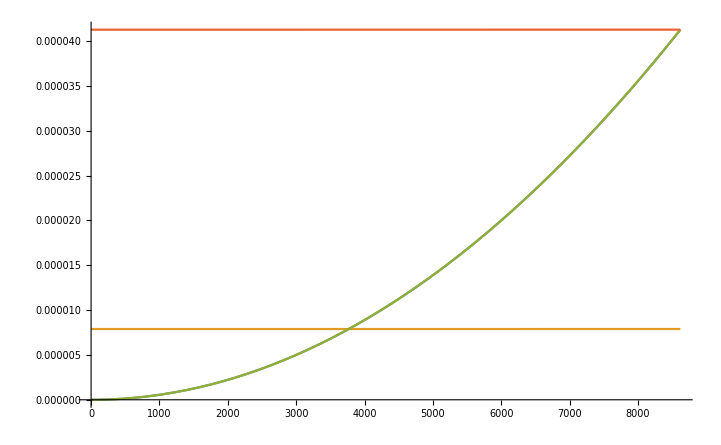

8619.78

```mathematica
inmχ = 100000.;
atomnumber=1;
Plot[{Emin[SR,u,inmχ,mN[[atomnumber]]],Emax[SR,u,inmχ,mN[[atomnumber]]],Emin[0,u,inmχ,mN[[atomnumber]]],Emax[0,u,inmχ,mN[[atomnumber]]]},{u,0,upintHS[inmχ,mN⟦atomnumber⟧]}]
upintHS[inmχ,mN[[atomnumber]]]
```

```mathematica
inmχ = 100000.;
inmA = 0.005;
inep = 10^-8;
inαχ = 0.024 inmχ/1000.;
σDD[mχ_,mA_,ϵ_,αχ_,mN_,ZN_,EN_]:=NIntegrate[
dσDDdE[0.5vgal,mχ,mA,ϵ,αχ,ER,mN,ZN,EN],
{ER,0,EDDmax[vgal,mχ,mN]},WorkingPrecision->5,Method-> {Automatic,"SymbolicProcessing"->0}];
mp=0.938272;
outσ=σDD[inmχ,inmA,inep,inαχ,mp,1.,EN[1.]](*m^2(1 pb)/(10^-40 m^2)*)
σDD[mχ_,mA_,ϵ_,αχ_,mN_,ZN_,EN_]:=NIntegrate[
dσDDdE[u,mχ,mA,ϵ,αχ,ER,mN,ZN,EN]integranduDD[u],{u,0,(*upint*)100upintHS[inmχ,mN]},
{ER,0,EDDmax[u,mχ,mN]},WorkingPrecision->5,Method-> {Automatic,"SymbolicProcessing"->0}]
outσ=σDD[inmχ,inmA,inep,inαχ,mp,1.,EN[1.]](*m^2(1 pb)/(10^-40 m^2)*)
```

1.3105×10^-38

4.1196×10^-39

7.14999×10^-64

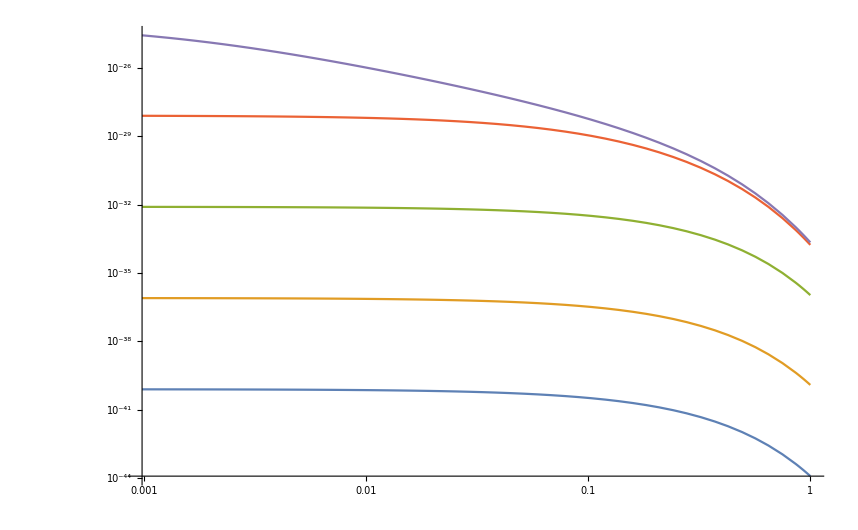

```mathematica
dσDDdE[u0,inmχ,inmA,inep,inαχ,5,mN⟦1⟧,ZN⟦1⟧,EN[AN⟦1⟧]]
LogLogPlot[{dσDDdE[u0,inmχ,500.,inep,inαχ,ER,mN⟦1⟧,ZN⟦1⟧,EN[AN⟦1⟧]],dσDDdE[u0,inmχ,50.,inep,inαχ,ER,mN⟦1⟧,ZN⟦1⟧,EN[AN⟦1⟧]],dσDDdE[u0,inmχ,5,inep,inαχ,ER,mN⟦1⟧,ZN⟦1⟧,EN[AN⟦1⟧]],dσDDdE[u0,inmχ,0.5,inep,inαχ,ER,mN⟦1⟧,ZN⟦1⟧,EN[AN⟦1⟧]],dσDDdE[u0,inmχ,0.05,inep,inαχ,ER,mN⟦1⟧,ZN⟦1⟧,EN[AN⟦1⟧]]},{ER,0,1}]
```

```mathematica
SetDirectory[NotebookDirectory[]];
AbsoluteTiming[tabepm10=Table[{10^lmA,τrat[10000.,10^lmA,10^-10,0.035 10000/1000]},{lmA,-3,0,0.001}];]
Export["1000tabepm10.csv",tabepm10,"CSV"];
tabepm10=Import["1000tabepm10.csv"]//ToExpression;
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

{796.156,Null}

```mathematica
tabep=Flatten[Table[{{tabepm10[[i,1]],10^lϵ},10^-10/10^lϵ tabepm10[[i,2]]},{i,1,Length[tabepm10]},{lϵ,-11.5,-7,0.01}],1];
```

```mathematica
itab=Interpolation[tabep,InterpolationOrder->1];
```

```mathematica
(*plot0=ContourPlot[itab[10^lmA,10^lϵ]==10^-6,{lmA,-3,0},{lϵ,-11.5,-7},PlotRange->All,ContourStyle-> Red,MaxRecursion-> 6];
plot1=ContourPlot[itab[10^lmA,10^lϵ]==10^-4,{lmA,-3,0},{lϵ,-11.5,-7},PlotRange->All,ContourStyle-> Orange,MaxRecursion-> 6];
plot2=ContourPlot[itab[10^lmA,10^lϵ]==10^-2,{lmA,-3,0},{lϵ,-11.5,-7},PlotRange->All,ContourStyle-> Brown,MaxRecursion-> 6];*)
plot3=ContourPlot[itab[10^lmA,10^lϵ]==10^-0,{lmA,-3,-0},{lϵ,-11.5,-7},PlotRange->All,ContourStyle-> Green,MaxRecursion-> 6];
(*plot4=ContourPlot[itab[10^lmA,10^lϵ]==10^2,{lmA,-3,-0},{lϵ,-11.5,-7},PlotRange->All,ContourStyle-> Blue,MaxRecursion->2];*)
```

```mathematica
Show[plot0,plot1,plot2,plot3,plot4,Frame-> True,FrameStyle-> Black,LabelStyle-> 10,FrameLabel-> {"Log10(mχ)","Log10(ϵ)"},Epilog-> {Text[Style["10^0",10],Scaled[{0.7,0.12}]],Text[Style["10^-2",10],Scaled[{0.2,0.15}]],Text[Style["10^-4",10],Scaled[{0.15,0.56}]]}]
```